```mathematica
(*http://reference.wolfram.com/language/tutorial/SolvingLinearSystems.zh.html*)
LinearSolve[{{1,2},{4,5}},{3,6}]
```

{-1,2}

```mathematica
p = {1,4};
q = {2,5};
```

```mathematica
p2=p * (-1)
```

{-1,-4}

```mathematica
q2=q * 2
```

{4,10}

```mathematica
v = p2 + q2
```

{3,6}

```mathematica
vectorGraphics[p_]:=Graphics[{Arrowheads[.07],Thickness[.01],Black,Arrow[{{0,0},p}]}]
```

```mathematica
g=vectorGraphics@p2;
```

```mathematica
g2=vectorGraphics@q2;
```

```mathematica
g3=vectorGraphics@v;
```

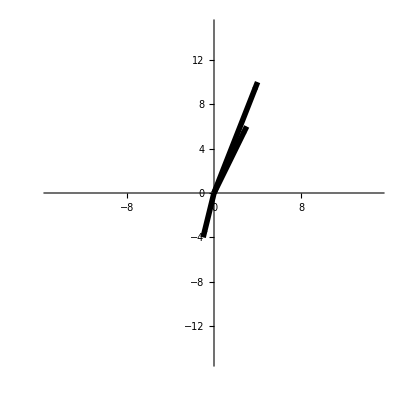

```mathematica
.
```

```mathematica
RowReduce[{{1,2,3},{4,5,6}}]//MatrixForm
```

(1 | 0 | -1
0 | 1 | 2)

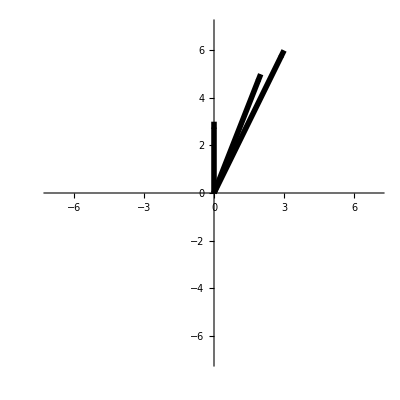

```mathematica
Show[vectorGraphics[{1,4} -1],vectorGraphics[{2,5}],vectorGraphics[{3,6}],PlotRange-> {{-7,7},{-7,7}},Axes-> True,AxesOrigin-> {0,0}]
```

```mathematica
RowReduce[{{3,1,a},{2,1,b}}]
```

{{1,0,a-b},{0,1,-2 a+3 b}}